Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 3. Frattali classici e L-sistemi

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 3.1 (Guarnizione di Sierpinski).

### Testo dell’esercizio

Disegnare le approssimazioni della guarnizione di Sierpinski, illustrata nella seguente figura.

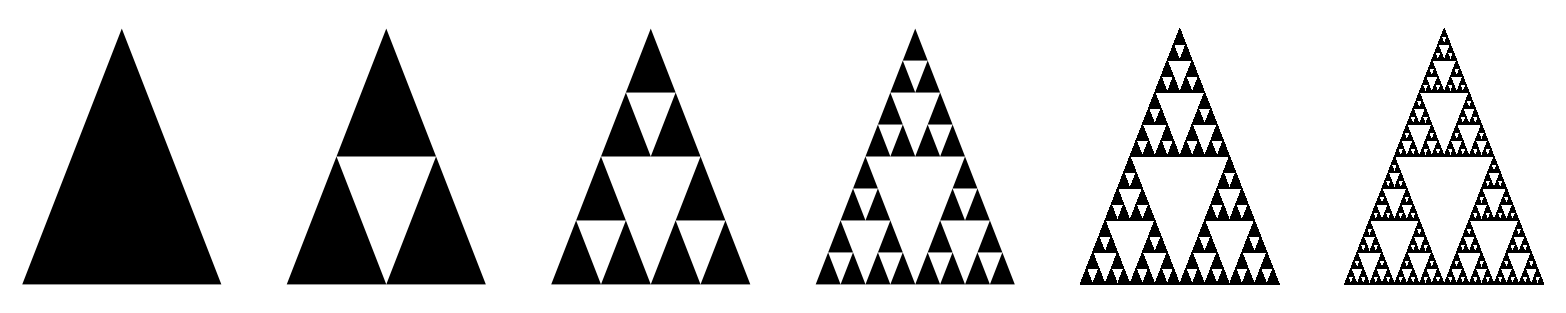

Mettere in evidenza la self-similarity, ingrandendo in modo opportuno una approssimazione e confrontandola con una precedente.

### Svolgimento

Definiamo il nostro insieme iniziale di terne cui applicheremo la sostituzione.

```mathematica
t0={{{0,0},{Cos[π/3],Sin[π/3]},{1,0}}};
```

Costruiamo, poi, una funzione che applichi la sostituzione richiesta ad ogni terna nella lista e sistemi correttamente le parentesi.

```mathematica
t[l_]:=Flatten[
ReplaceAll[
#,
{p1_,p2_,p3_}->{{p1,(p1+p2)/2,(p1+p3)/2},{(p1+p2)/2,p2,(p2+p3)/2},{(p1+p3)/2,(p2+p3)/2,p3}}
]&/@l,
1
]
```

Applichiamo, infine, un certo numero di volte la trasformazione t alla lista iniziale.

```mathematica
GraphicsRow[Graphics/@Triangle/@NestList[t,t0,5],ImageSize->Full]
```

```mathematica
GraphicsRow[
Join[
{Graphics[Triangle[t0]]},
Drop[Graphics/@Triangle/@NestList[t,t0,7],{1}]/.Graphics[j__]->Graphics[j,Epilog->{Blue,Thin,Line[{{0.2,0.433},{0.8,0.433},{0.8,0.866},{0.2,0.866},{0.2,0.433}}]}]
],
ImageSize->Full]
```